```mathematica
ClearAll["Global`*"]
```

```mathematica
This notebook is a companion to the article [arxiv number]. It contains interactive plots that demonstrate the evolution of the quasinormal frequencies (QNFs), calculated using the semi-classical method presented by Gonzalez, Papantonopoulos, Saavedra and Vasquez, for the allowed values of (M,Q) corresponding to the phase space (the  "sharkfin" diagram)  drawn for Subscript[L^2, dS]=3/Λ=1.  This parametrisation is used throughout the notebook. 

DO NOT CHANGE the Λ=3 input - it will render most of this notebook useless !

Section 1 contains the preamble needed to draw the sharkfin diagram, the explicit definitions of the horizons and the surface gravities thereof, as well as the minutiae for the aesthetics of the plot diagrams.

Section 2 imports the necessary notebooks for subsequent calculations: the QNF computations and the WKB notebook against which we can compare our output. 
A small comment on the notarion: QNFminus in this notebook = "black hole (event horizon) family" =  SubPlus[ω] in the manuscript; QNMplus in this notebook = "cosmological (horizon) family" = Subscript[ω, c] in the manuscript.

To use this notebook, you must first evaluate sections 1 and 2 !

Section 3 plots the interactive sharkfin plot: it allows the user to observe the behaviour of the QNM potential on the physically-relevant domain between event and cosmological horizon (i.e. on SubPlus[r]<=r<=Subscript[r, c]), the "locations" of the horizons, and the corresponding QNF values for the "black hole" and "cosmological" QNFs. 

Section 4 compares the QNFs calculated here with those calculated using Konoplya's WKB package. 

Section 5 shows how the imaginary component of the QNF scales with the mass of the scalar field. We demonstrate how we determine the "critical mass" Subscript[μ, crit] visually and directly.

Section 6 highlights the parameter space in which the semi-classical method predicts instability (Im{ω}<0) and superradiance  (qQ/Subscript[r, c]<Re{ω}<qQ/SubPlus[r]) .
Section 7 highlights the parameter space in which there is evidence for the violation of strong cosmic censorship (SCC) (-(Im{ω})/(|SubMinus[κ]|)>1/2) .
```

1) Defining the parameter space of the RNdS black hole space-time

```mathematica
g[r_]=1-(2 M)/r+Q^2/r^2-Λ/3 r^2;
```

```mathematica
(*   What are the constraints on M and Q for the 4D RNdS black hole ?  *)
```

```mathematica
Discriminant[(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)*(-r^2),r];
```

```mathematica
Solve[(-16/27 (-9 M^2 Λ+9 Q^2 Λ+81 M^4 Λ^2-108 M^2 Q^2 Λ^2+24 Q^4 Λ^2+16 Q^6 Λ^3))==0,M]; (* solve for constraints on M *)
```

```mathematica
1/M^2*(1+1/3*(M^2*Λ)+4/9*(M^2*Λ)^2+8/9*(M^2*Λ)^3)/.{M->Sqrt[2/27],Λ->3}; (* this returns the constraint on Q*)
```

```mathematica
(* How do we locate the horizons ? Let us set the dS horizon to 1. *)
```

```mathematica
Solve[(g[r]/.Λ->3/LdS^2/.LdS->1)==0,r][[1,1,2]]//Simplify;
```

```mathematica
r412=1/6 (-√3 √((-12 Q^2+(1+(-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))^2)/((-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3)))+3 √(4/3+(-1+12 Q^2)/(3 (-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))-1/3 (-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3)+(4 √3 M)/(√((-12 Q^2+(1+(-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))^2)/((-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))))));(* inner horizon *)
```

```mathematica
r312=1/6 (-√3 √((-12 Q^2+(1+(-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))^2)/((-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3)))-3 √(4/3+(-1+12 Q^2)/(3 (-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))-1/3 (-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3)+(4 √3 M)/(√((-12 Q^2+(1+(-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))^2)/((-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))))));(* unphysical horizon *)
```

```mathematica
r212=1/6 (√3 √((-12 Q^2+(1+(-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))^2)/((-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3)))+3 √(4/3+(-1+12 Q^2)/(3 (-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))-1/3 (-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3)-(4 √3 M)/(√((-12 Q^2+(1+(-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))^2)/((-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3)))))); (* cosmological horizon *)
```

```mathematica
r112=1/6 (√3 √((-12 Q^2+(1+(-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))^2)/((-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3)))-3 √(4/3+(-1+12 Q^2)/(3 (-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))-1/3 (-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3)-(4 √3 M)/(√((-12 Q^2+(1+(-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3))^2)/((-1+54 M^2-36 Q^2-6 √3 √(27 M^4-M^2 (1+36 Q^2)+(Q+4 Q^3)^2))^(1/3)))))); (* event horizon *)
```

```mathematica
qext=r112*Sqrt[(1+2*(r112/r212))/(1+2*(r112/r212)+3*(r112/r212)^2)]; (* extremal charge, as defined in Eq. (2.5) of  Dias et al.https://arxiv.org/abs/1808.04832Nonehttps://arxiv.org/abs/1808.04832HyperlinkActionRecycledHyperlinkActive *)
```

```mathematica
kminus=1/2*D[(g[r]/.Λ->3),r]/.r->r412; (* surface gravity at the inner horizon *)
kplus=1/2*D[(g[r]/.Λ->3),r]/.r->r112; (* surface gravity at the event horizon *)
kcosm=1/2*D[(g[r]/.Λ->3),r]/.r->r212; (* surface gravity at the cosmological horizon *)
```

```mathematica
(* How do we draw the sharkfin ? *)
```

```mathematica
RNdS=Discriminant[-Q^2+2 M r-r^2+r^4,r];
```

```mathematica
sharkfin[M_,Q_]=ContourPlot[{RNdS==0,M==Q},{M,0,0.28},{Q,0,0.31},PlotRange->{{-0.037,0.385},{-0.03,0.33}},
(* Beyond this point, we define the aesthetics of the plot *)
ContourStyle->Thread[Directive[{Black,Green},Thick]],PlotTheme->"Monochrome",BoundaryStyle->Thick,ContourStyle->Thick,WorkingPrecision->100,GridLines->None,FrameStyle->Directive[Gray],FrameTicksStyle->Directive[10,FontFamily->"Helvetica"],FrameLabel->{Style[ M,22,Black,Bold,FontFamily->"TeX Gyre Pagella"],Style[Q,22,Black,Bold,FontFamily->"TeX Gyre Pagella"]},ImageSize->Medium,ContourLabels->Automatic,PlotLegends->Placed[{Style["Δ = 0",16,FontFamily->"TeX Gyre Pagella"],Style["M = Q",14,FontFamily->"TeX Gyre Pagella"]},{Scaled[{0.03,0.97}],{0.03,0.97}}],Epilog->{{Black,PointSize[Large],Point[{0,0}],Text[Style["O " Invisible[""][0 ,0],Black,Bold,12,FontFamily->"TeX Gyre Pagella"],{-0.035,-0.02},{-1.4,-1}]},{Black,
PointSize[Large],Point[{(√2)/(3 √3),1/(2 √3)}],Text[Style["U " Invisible[""][HoldForm[(√2)/(3 √3)] ,HoldForm[1/(2 √3)]],Black,Bold,12,FontFamily->"TeX Gyre Pagella",ScriptLevel->1],{0.315,0.3},{0,0}]},{Black,PointSize[Large],Point[{1/(3 √3) , 0}],Text[Style["N " Invisible[""][1/(3 √3) , 0],Black,Bold,12,FontFamily->"TeX Gyre Pagella",ScriptLevel->1],{1/(3 √3),-0.025},{-1.4,-1}]},{Black,PointSize[Large],Point[{1/4,1/4}],Text[Style["E " Invisible[""][1/4 , 1/4],Black,Bold,12,FontFamily->"TeX Gyre Pagella",ScriptLevel->1],{0.275,0.247},{0,0}]},{Directive[Black,Thick],Line[{{0,0},{1/(3 √3),0}}]}}];
```

```mathematica
pts={{0.14,0.14},{(√2)/(3 √3),1/(2 √3)},{1/4,1/4}};
fill=RegionPlot[ConvexHullMesh[pts],AspectRatio->1/GoldenRatio,BoundaryStyle->Directive[Purple,Thick],PlotStyle->Purple];
fin2=ContourPlot[{M==Q},{M,0,0.285},{Q,0,0.31},PlotRange->{{-0.037,0.385},{-0.03,0.33}},ContourStyle->Thread[Directive[{Green},Thick,Dashed]],PlotTheme->"Monochrome",BoundaryStyle->Thick,ContourStyle->Thick,WorkingPrecision->100,GridLines->None,FrameStyle->Directive[Gray],FrameTicksStyle->Directive[10,FontFamily->"Helvetica"]];

RNdSsharkfin[M,Q]=Show[sharkfin[M,Q],fill,fin2];
```

```mathematica
(* New additions: trims and tricks for the superradiance / stability plots *)
```

```mathematica
outline=RegionPlot[{Discriminant[-Q^2+2 M r-r^2+r^4,r]<=0},{M,0,0.33},{Q,0,0.33},BoundaryStyle->None,PlotStyle->White,PlotPoints->100];
```

```mathematica
sharklight=ContourPlot[{RNdS==0,M==Q},{M,0,0.28},{Q,0,0.31},PlotRange->{{-0.01,0.3},{-0.01,0.33}},PlotTheme->"Scientific",GridLines->None,FrameLabel->{Style[ M,Large,Black,FontFamily->"TeX Gyre Pagella"],Style[Q,Large,Black,FontFamily->"TeX Gyre Pagella"]},ImageSize->Medium,ContourLabels->Automatic,ContourStyle->Thread[Directive[{Purple,Green},Thick]]];
sharklight2=ContourPlot[{RNdS==0,M==Q},{M,0,0.28},{Q,0,0.31},PlotRange->{{-0.037,0.385},{-0.03,0.33}},PlotTheme->"Scientific",GridLines->None,FrameLabel->{Style[ M,Large,Black,FontFamily->"TeX Gyre Pagella"],Style[Q,Large,Black,FontFamily->"TeX Gyre Pagella"]},ImageSize->Medium,PlotPoints->100,ContourLabels->Automatic,ContourStyle->Thread[Directive[{Purple,Green},Thick]]];
```

#### 2) Notebooks for QNF computations based on the method of Papantonopoulos et al. and the WKB notebook of Konoplya.

```mathematica
Veffmq[r_,l_,M_,Q_,Λ_,μ_,c_,w_]=(g[r]*((l (l+1))/r^2+D[g[r],r]/r+μ^2)-2 w c (-Q)/r-(c^2 Q^2)/r^2)/.Λ->3/LdS^2/.LdS->1;
```

```mathematica
Import[NotebookDirectory[]<>"WKB_RNdS_Papantonopoulos.m"];
(*Two families of solutions. As explained by Dias et al.https://arxiv.org/abs/1808.04832Nonehttps://arxiv.org/abs/1808.04832HyperlinkActionRecycledHyperlinkActive, these correspond to the event horizon (r=r_+) and cosmological horizon (r=Subscript[r, c])*)
(*cosmological horizon*)QNMplus[M_,Q_]=wplus1*L+wzero+wneg1plus/L+wneg2/L^2;
(*event horizon*)  QNMminus[M_,Q_]=wminus1*L+wzero+wneg1minus/L+wneg2/L^2;
```

```mathematica
Import[NotebookDirectory[]<>"WKB.m"];
```

#### 3) The interactive sharkfin: how the horizons, QNM potential, and QNFs evolve

```mathematica
(* Inspired by this comment from Robert McHughhttps://community.wolfram.com/groups/-/m/t/1898533Nonehttps://community.wolfram.com/groups/-/m/t/1898533HyperlinkActionRecycledHyperlinkActive *)
DynamicModule[{bt={{0.33,0.33}},loc},loc=Graphics[{PointSize[Small],LightBlue,Point[bt]},PlotRange->{{-0.037,0.385},{-0.03,0.33}}];
{LocatorPane[Dynamic[bt],Dynamic@Show[{RNdSsharkfin[M,Q],loc},ImageSize->Medium],LocatorAutoCreate->True],Dynamic@Manipulate[Block[{M=bt[[1,1]],Q=bt[[1,2]],Λ=3,L=Sqrt[l*(l+1)],c=q,μ=m},Show[Plot[ComplexExpand[Re[Veffmq[r,l,M,Q,3,μ,c,QNFminus]/.M->bt[[1,1]]/.Q->bt[[1,2]]]],{r,0,1},GridLines->None,FrameStyle->Directive[Gray],FrameTicksStyle->Directive[10,FontFamily->"Helvetica"],PlotTheme->"Scientific",PlotRange->{{-0.2,1},{-1,ymax}},
(* ymax on the potential accommodates the growing and shrinking amplitude *)FrameLabel->{Style["r",18,Black,FontFamily->"TeX Gyre Pagella"],Style["V",18,Black,FontFamily->"Tex Gyre Pagella"]},PlotStyle->{Directive[Black,Thick]},ImageSize->Medium],ContourPlot[{r==Re[(r112/.M->bt[[1,1]]/.Q->bt[[1,2]])],r==Re[(r212/.M->bt[[1,1]]/.Q->bt[[1,2]])],r==Re[(r312/.M->bt[[1,1]]/.Q->bt[[1,2]])],r==Re[(r412/.M->bt[[1,1]]/.Q->bt[[1,2]])]},{r,0,1},{V,-1000,1000},PlotLegends->{"r112 = r_+","r212 = r_c","r312 = -(r_-+r_++r_c)","r412 = r_-"}]]],{m,0,10},{q,0,2},{l,1,20},{ymax,1,100},Paneled->t],Dynamic@Grid[Prepend[{{bt[[1,1]],bt[[1,2]],bt[[1,2]]/bt[[1,1]]}},{Style["M",Medium,FontFamily->"TeX Gyre Pagella"],Style["Q",Medium,FontFamily->"TeX Gyre Pagella"],Style["Q/M",Medium,FontFamily->"TeX Gyre Pagella"]}],Frame->All],Dynamic@Manipulate[
Block[{M=bt[[1,1]],Q=bt[[1,2]],Λ=3,L=Sqrt[l*(l+1)],μ=m,c=q},Grid[Prepend[{{Re[QNMminus[M,Q]],Im[QNMminus[M,Q]],Re[QNMplus[M,Q]],Im[QNMplus[M,Q]]}},{"Re[ω_minus]","Im[ω_minus]","Re[ω_plus]","Im[ω_plus]"}],Frame->All]],{m,0,10},{q,0,2},{l,1,20},Paneled->t],Dynamic@Grid[Prepend[{{(Re[r112/.M->bt[[1,1]]/.Q->bt[[1,2]]]),(Re[r212/.M->bt[[1,1]]/.Q->bt[[1,2]]]),(Re[r312/.M->bt[[1,1]]/.Q->bt[[1,2]]]),(Re[r412/.M->bt[[1,1]]/.Q->bt[[1,2]]]),(Re[Sqrt[1/6*(1+Sqrt[1-12*Q^2])]/.Q->bt[[1,2]]]),(Re[qext/.M->bt[[1,1]]/.Q->bt[[1,2]]])}},{Style["r112 = r_+",Medium,FontFamily->"TeX Gyre Pagella"],Style["r212 = r_c",Medium,FontFamily->"TeX Gyre Pagella"],Style["r312 = -(r_-+r_++r_c)",Medium,FontFamily->"TeX Gyre Pagella"],Style["r412 = r_-",Medium,FontFamily->"TeX Gyre Pagella"],(* nuumbers following r refer to item number in the list of solutions to f(r)=0; r312 is unphysical *)Style["r_c(Q) on Nariai branchhttps://arxiv.org/abs/1910.01648Nonehttps://arxiv.org/abs/1910.01648HyperlinkActionRecycledHyperlinkActive",Medium,FontFamily->"TeX Gyre Pagella"],Style["r_+~Q_ext on extremal branchhttps://arxiv.org/abs/1801.09694Nonehttps://arxiv.org/abs/1801.09694HyperlinkActionRecycledHyperlinkActive",Medium,FontFamily->"TeX Gyre Pagella"]}],Frame->All]}]
```

#### 4) QNF computations: checks and cross-checks

```mathematica
(* Choose your (M,Q) pair of input variables from the sharkfin and check against Konoplya's WKB for the uncharged massive scalar field in RNdS space=time*)
V[r_]=ComplexExpand[Re[Veffmq[r,l,M,Q,Λ,μ,c,w]]];
```

```mathematica
Grid[Prepend[
Block[{M=0.172,Q=0.079,Λ=3,L=Sqrt[l*(l+1)],μ=0,c=0,l=1,d=4,n=0,iprec=40},Table[{l,Re[QNMplus[M,Q]],Im[QNMplus[M,Q]],Re[WKBFormula[6,V[r],f[r],{r,0.4},n,iprec]//First//N],Im[WKBFormula[6,V[r],f[r],{r,0.4},n,iprec]//First//N],((Re[WKBFormula[6,V[r],f[r],{r,3M},n,iprec]//First//N]-Re[QNMplus[M,Q]])/Re[WKBFormula[6,V[r],f[r],{r,3M},n,iprec]//First//N])*100,((Im[WKBFormula[6,V[r],f[r],{r,3M},n,iprec]//First//N]-Im[QNMplus[M,Q]])/Im[WKBFormula[6,V[r],f[r],{r,3M},n,iprec]//First//N])*100//N},{l,1,5}]],{"l","Re[QNMplus]","Im[QNMplus]","Re[QNMwkb]","Im[QNMwkb]","%ErrRe","%ErrIm"}],Frame->{{True},{True}}]
```

l | Re[QNMplus] | Im[QNMplus] | Re[QNMwkb] | Im[QNMwkb] | %ErrRe | %ErrIm
1 | 0.815046 | -0.303212 | 0.815192 | -0.304317 | 0.0178122 | 0.363075
2 | 1.43433 | -0.292778 | 1.43588 | -0.292902 | 0.107895 | 0.0424831
3 | 2.03645 | -0.290169 | 2.03907 | -0.290276 | 0.128297 | 0.0366381
4 | 2.63318 | -0.289126 | 2.63665 | -0.289247 | 0.131701 | 0.0419015
5 | 3.2275 | -0.288604 | 3.23179 | -0.288736 | 0.132575 | 0.0457236

```mathematica
(* compare against QNM families quoted in the literaturehttps://arxiv.org/abs/1711.10502Nonehttps://arxiv.org/abs/1711.10502HyperlinkActionRecycledHyperlinkActive *)
```

```mathematica
DynamicModule[{bt={{0.33,0.33}},loc},loc=Graphics[{PointSize[Small],LightBlue,Point[bt]},PlotRange->{{-0.01,0.33},{-0.01,0.33}}];
{LocatorPane[Dynamic[bt],Dynamic@Show[{RNdSsharkfin[M,Q],loc},ImageSize->Medium],LocatorAutoCreate->True],Dynamic@Grid[Prepend[bt,{Style["M",Medium,FontFamily->"TeX Gyre Pagella"],Style["Q",Medium,FontFamily->"TeX Gyre Pagella"]}],Frame->All],
Dynamic@Manipulate[
Block[{M=bt[[1,1]],Q=bt[[1,2]],rm=r412,rn=r312,rp=r112,rc=r212,Λ=3,L=Sqrt[l*(l+1)],l=ell,μ=m,c=q,n=0},Grid[Prepend[{{Re[QNMminus[M,Q]],Im[QNMminus[M,Q]],Re[QNMplus[M,Q]],Im[QNMplus[M,Q]],-(n+1+l)*Abs[Re[ComplexExpand[kminus]]],-(n+1+l)*Abs[Re[ComplexExpand[kplus]]],-l*Abs[Re[ComplexExpand[kcosm]]],Im[-I*(n+1/2)*Abs[Re[ComplexExpand[kplus]]]]}},{"Re[ω_minus]","Im[ω_minus]","Re[ω_plus]","Im[ω_plus]","iω_(NE-)","iω_(NE+)","iω_dS","iω_Nariai"}],Frame->All]],{m,0,10},{q,0,2},{ell,1,20},Paneled->t]}]
```

#### 5) Im{ω} vs μ : finding the “critical mass”

```mathematica
DynamicModule[{bt={{0.33,0.33}},loc},loc=Graphics[{PointSize[Small],LightBlue,Point[bt]},PlotRange->{{-0.01,0.33},{-0.01,0.33}}];
{LocatorPane[Dynamic[bt],Dynamic@Show[{RNdSsharkfin[M,Q],loc},ImageSize->Medium],LocatorAutoCreate->True],Dynamic@Manipulate[Block[{M=bt[[1,1]],Q=bt[[1,2]],Λ=3,L=Sqrt[l*(l+1)],c=q,μ=m},
Plot[{-Im[QNMminus[M,Q]/.l->5],-Im[QNMminus[M,Q]/.l->10],-Im[QNMminus[M,Q]/.l->20],-Im[QNMminus[M,Q]/.l->30]},{μ,0,3},PlotStyle->{{Darker[Green,0.5],Thick},{Magenta,Thick},{Lighter[Blue,0.5],Thick},{Orange,Thick}},GridLines->None,FrameLabel->{Style["μ",Medium,FontFamily->"TeX Gyre Pagella"],Style["-Im[ω]",Medium,FontFamily->"TeX Gyre Pagella"]},PlotTheme->"Scientific",PlotLegends->{Style["l=5",Medium,FontFamily->"TeX Gyre Pagella"],Style["l=10",Medium,FontFamily->"TeX Gyre Pagella"],Style["l=20",Medium,FontFamily->"TeX Gyre Pagella"],Style["l=30",Medium,FontFamily->"TeX Gyre Pagella"]}]],{q,0,20},Paneled->t],Dynamic@Grid[Prepend[{{bt[[1,1]],bt[[1,2]],bt[[1,2]]/bt[[1,1]]}},{Style["M",Medium,FontFamily->"TeX Gyre Pagella"],Style["Q",Medium,FontFamily->"TeX Gyre Pagella"],Style["Q/M",Medium,FontFamily->"TeX Gyre Pagella"]}],Frame->All]}]
```

```mathematica
(* For this set of (M,Q) parameters, we obtain the same result for the critical mass, irrespective of scalar field charge.That Q=0 is a factor that we should not dismiss.*) Block[{M=0.19245,Q=0,Λ=3,L=Sqrt[l*(l+1)],c=5},Solve[(Refine[Im[ComplexExpand[QNMminus[M,Q]/.l->10]],Assumptions->μ>0])==(Refine[Im[ComplexExpand[QNMminus[M,Q]/.l->20]],Assumptions->μ>0]),μ]
]
```

{{μ→-1.40831},{μ→1.40831}}

```mathematica
·
```

#### 6) Do we observe a super-radiance and/or instability (section 3.2)?

```mathematica
DynamicModule[{bt={{0.33,0.33}},loc},loc=Graphics[{PointSize[Small],LightBlue,Point[bt]},PlotRange->{{-0.01,0.33},{-0.01,0.33}}];
{LocatorPane[Dynamic[bt],Dynamic@Show[{RNdSsharkfin[M,Q],loc},ImageSize->Medium],LocatorAutoCreate->True],
(* Superradiant instability: Im[ω] > 0 when qQ/Subscript[r, c] < ω < qQ/(r_+) *)Dynamic@Manipulate[Block[{M=bt[[1,1]],Q=bt[[1,2]],Λ=3,L=Sqrt[l*(l+1)],c=q,μ=m},Grid[Prepend[{{(c*bt[[1,2]])/(Re[r212/.M->bt[[1,1]]/.Q->bt[[1,2]]]),ComplexExpand[Re[QNMminus[M,Q]/.M->bt[[1,1]]/.Q->bt[[1,2]]]],ComplexExpand[Re[QNMplus[M,Q]/.M->bt[[1,1]]/.Q->bt[[1,2]]]],(c*bt[[1,2]])/(Re[r112/.M->bt[[1,1]]/.Q->bt[[1,2]]])}},{Style["qQ/r_c",Medium,FontFamily->"TeX Gyre Pagella"],Style["< ω_+ <",Medium,FontFamily->"TeX Gyre Pagella"],Style["< ω_c <",Medium,FontFamily->"TeX Gyre Pagella"],Style["qQ/(r_+)",Medium,FontFamily->"TeX Gyre Pagella"]}],Frame->All]],{q,0,20},{m,0,20},{l,1,20},Paneled->t],Dynamic@Grid[Prepend[bt,{Style["M",Medium,FontFamily->"TeX Gyre Pagella"],Style["Q",Medium,FontFamily->"TeX Gyre Pagella"]}],Frame->All],Dynamic@Grid[Prepend[{{(Re[r112/.M->bt[[1,1]]/.Q->bt[[1,2]]]),(Re[r212/.M->bt[[1,1]]/.Q->bt[[1,2]]])}},{Style["r112 = r_+",Medium,FontFamily->"TeX Gyre Pagella"],Style["r212 = r_c",Medium,FontFamily->"TeX Gyre Pagella"]}],Frame->All],Dynamic@Manipulate[Block[{M=bt[[1,1]],Q=bt[[1,2]],Λ=3,L=Sqrt[l*(l+1)],c=q,μ=m},Show[Plot[ComplexExpand[Re[Veffmq[r,l,M,Q,3,μ,c,QNFminus]/.M->bt[[1,1]]/.Q->bt[[1,2]]]],{r,0,5},GridLines->None,FrameStyle->Directive[Gray],FrameTicksStyle->Directive[10,FontFamily->"Helvetica"],PlotTheme->"Scientific",PlotRange->{{-0.2,5},{-ymax,ymax}},FrameLabel->{Style["r",18,Black,FontFamily->"TeX Gyre Pagella"],Style["V",18,Black,FontFamily->"Tex Gyre Pagella"]},PlotStyle->{Directive[Black,Thick]},ImageSize->Medium],ContourPlot[{r==Re[(r112/.M->bt[[1,1]]/.Q->bt[[1,2]])],r==Re[(r212/.M->bt[[1,1]]/.Q->bt[[1,2]])],r==Re[(r312/.M->bt[[1,1]]/.Q->bt[[1,2]])],r==Re[(r412/.M->bt[[1,1]]/.Q->bt[[1,2]])]},{r,0,1},{V,-1000,1000},PlotLegends->{"r112 = r_+","r212 = r_c","r312 = -(r_-+r_++r_c)","r412 = r_-"}]]],{m,0,20},{q,0,20},{l,1,20},{ymax,1,100},Paneled->t]
}]
```

```mathematica
(* The criterion for instability that we consider here is Im[ω]>0 i.e. growing modes*)
```

```mathematica
Manipulate[Block[{Λ=3,L=Sqrt[l*(l+1)],c=q,μ=m},
growing=RegionPlot[{ComplexExpand[Im[QNMminus[M,Q]]]>0,ComplexExpand[Im[QNMplus[M,Q]]]>0,ComplexExpand[Im[QNMminus[M,Q]]]>0&&ComplexExpand[Im[QNMplus[M,Q]]]>0},{M,0,0.33},{Q,0,0.33},BoundaryStyle->None,PlotStyle->{Darker[LightBlue,0.1],Lighter[Orange,0.5],Lighter[Magenta,0.7]},PlotPoints->50,PlotLegends->Placed[SwatchLegend[{Lighter[Magenta,0.7],Darker[LightBlue,0.1],Lighter[Orange,0.5]},{Style["Im[ω_+] > 0 ∪ Im[ω_c] > 0",18,FontFamily->"TeX Gyre Pagella"],Style["Im[ω_+] > 0",18,FontFamily->"TeX Gyre Pagella"],Style["Im[ω_c] > 0",18,FontFamily->"TeX Gyre Pagella"]}],{Left,Top}]];
(* Note: please give Mathematica a few moments to render the plot after changing scalar field parameters *)
Show[sharklight,fill,fin2,growing,outline,sharklight2]],{m,0,20},{q,0,20},{l,1,20},Paneled->t]
```

```mathematica
(* The criterion for superradiance that we consider here is qQ/Subscript[r, c] < Re[ω] < qQ/(r_+) *)
Manipulate[Block[{Λ=3,L=Sqrt[l*(l+1)],c=q,μ=m},
SR=RegionPlot[{(c Q)/ComplexExpand[Re[r212]]<ComplexExpand[Re[QNMminus[M,Q]]]<(c Q)/ComplexExpand[Re[r112]],(c Q)/ComplexExpand[Re[r212]]<ComplexExpand[Re[QNMplus[M,Q]]]<(c Q)/ComplexExpand[Re[r112]]},{M,0,0.33},{Q,0,0.33},PlotPoints->100,BoundaryStyle->None,PlotStyle->{Darker[LightBlue,0.1],Lighter[Orange,0.5]},PlotLegends->Placed[{Style["(c Q)/r_c < Re[ω_+] < (c Q)/(r_+)",18,FontFamily->"TeX Gyre Pagella"],Style["(c Q)/r_c < Re[ω_c] < (c Q)/(r_+)",18,FontFamily->"TeX Gyre Pagella"]},{Left,Top}]];
(* Note: please give Mathematica a few moments to render the plot after changing scalar field parameters *)
Show[sharklight,fill,fin2,SR,outline,sharklight2]],{m,0,20},{q,0,20},{l,1,20},Paneled->t]
```

#### 7) Is the SCC conjecture violated (section 3.3)?

```mathematica
DynamicModule[{bt={{0.33,0.33}},loc},loc=Graphics[{PointSize[Small],LightBlue,Point[bt]},PlotRange->{{-0.01,0.33},{-0.01,0.33}}];
{LocatorPane[Dynamic[bt],Dynamic@Show[{RNdSsharkfin[M,Q],loc},ImageSize->Medium],LocatorAutoCreate->True],Dynamic@Manipulate[Block[{M=bt[[1,1]],Q=bt[[1,2]],Λ=3,L=Sqrt[l*(l+1)],c=q,μ=m},
Plot[{(-Im[QNMminus[M,Q]/.l->5])/Abs[Re[ComplexExpand[kminus]]],(-Im[QNMminus[M,Q]/.l->10])/Abs[Re[ComplexExpand[kminus]]],(-Im[QNMminus[M,Q]/.l->20])/Abs[Re[ComplexExpand[kminus]]],(-Im[QNMminus[M,Q]/.l->30])/Abs[Re[ComplexExpand[kminus]]]},{μ,0,3},PlotStyle->{{Darker[Green,0.5],Thick},{Magenta,Thick},{Lighter[Blue,0.5],Thick},{Orange,Thick}},GridLines->None,FrameLabel->{Style["μ",Medium,FontFamily->"TeX Gyre Pagella"],Style["(-Im[ω])/(|SubscriptBox[κ, -]|)",Medium,FontFamily->"TeX Gyre Pagella"]},PlotTheme->"Scientific",PlotLegends->{Style["l=5",Medium,FontFamily->"TeX Gyre Pagella"],Style["l=10",Medium,FontFamily->"TeX Gyre Pagella"],Style["l=20",Medium,FontFamily->"TeX Gyre Pagella"],Style["l=30",Medium,FontFamily->"TeX Gyre Pagella"]}]],{q,0,20},Paneled->t],Dynamic@Grid[Prepend[{{bt[[1,1]],bt[[1,2]],bt[[1,2]]/bt[[1,1]]}},{Style["M",Medium,FontFamily->"TeX Gyre Pagella"],Style["Q",Medium,FontFamily->"TeX Gyre Pagella"],Style["Q/M",Medium,FontFamily->"TeX Gyre Pagella"]}],Frame->All]}]
```

```mathematica
(* To view the parameter space where SCC appears violated, select your scalar field parameters and evaluate the cell below.
Here, we choose μ=1, q=0.1, l=1 (i.e. Fig. 9a). 
ONLY modify the definitions of μ,q, l, as indicated. 
*)
```

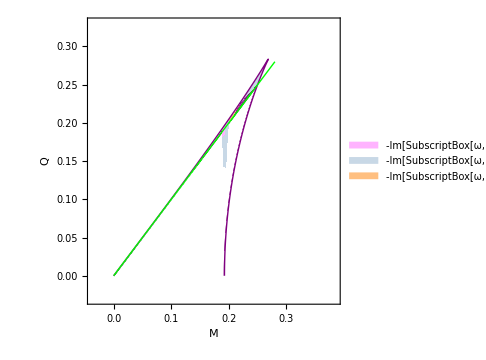

```mathematica
SCCmu1c01L1=Block[{Λ=3,L=Sqrt[l*(l+1)],c=q,(* choose your parameters here *) μ=1,q=0.1,l=1(*parameters have been selected; time to evaluate the cell *)},
z=RegionPlot[{(-Im[QNMminus[M,Q]])/Abs[ComplexExpand[Re[kminus]]]>1/2,(-Im[QNMplus[M,Q]])/Abs[ComplexExpand[Re[kminus]]]>1/2,(-Im[QNMminus[M,Q]])/Abs[ComplexExpand[Re[kminus]]]>1/2&&(-Im[QNMplus[M,Q]])/Abs[ComplexExpand[Re[kminus]]]>1/2},{M,0,0.33},{Q,0,0.33},BoundaryStyle->None,PlotStyle->{Darker[LightBlue,0.1],Lighter[Orange,0.5],Lighter[Magenta,0.7]},PlotPoints->50,PlotLegends->Placed[SwatchLegend[{Lighter[Magenta,0.7],Darker[LightBlue,0.1],Lighter[Orange,0.5]},{Style["-Im[SubscriptBox[ω, +]]/(|SubscriptBox[κ, -]|) > 1/2 ∪ -Im[SubscriptBox[ω, c]]/(|SubscriptBox[κ, -]|) > 1/2",18,FontFamily->"TeX Gyre Pagella"],Style["-Im[SubscriptBox[ω, +]]/(|SubscriptBox[κ, -]|) > 1/2",18,FontFamily->"TeX Gyre Pagella"],Style["-Im[SubscriptBox[ω, c]]/(|SubscriptBox[κ, -]|) > 1/2",18,FontFamily->"TeX Gyre Pagella"]}],{Left,Top}],FrameTicksStyle->16]];
plotSCCmu1c01L1=Show[sharklight2,fill,fin2,SCCmu1c01L1,outline,sharklight2]
```